```mathematica
D[(x-a)/(b-a)b/x,x]
```

b/((-a+b) x)-(b (-a+x))/((-a+b) x^2)

```mathematica
Simplify[b/((-a+b) x)-(b (-a+x))/((-a+b) x^2)]
```

-(a b)/((a-b) x^2)

```mathematica
D[(-x-a)/(b-a)b/-x,x]
```

(b (-a-x))/((-a+b) x^2)+b/((-a+b) x)

```mathematica
Simplify[(b (-a-x))/((-a+b) x^2)+b/((-a+b) x)]
```

(a b)/((a-b) x^2)

-(a b)/((a-b) x^2)

```mathematica
(a b)/((a-b) b^2)
```

a/((a-b) b)

```mathematica
Maximize[]
```

```mathematica
f[x_]:=1+1/2*(-x^2*Log[x^2]-(1/2-x^2)*Log[1/2-x^2]+(1/4+x^2)*Log[1/4+x^2]+(3/4-x^2)*Log[3/4-x^2]+(3/8+1/8*Sqrt[16*x^2+1])*Log[3/8+1/8*Sqrt[16*x^2+1]]+(3/8-1/8*Sqrt[16*x^2+1])*Log[3/8-1/8*Sqrt[16*x^2+1]])/Log[2]
```

```mathematica
f[0.66]
```

0.711863

```mathematica
NMaximize[f[x],x]
```

NMaximize::nrnum: The function value -0.785388-0.293164 ⅈ is not a real number at {x} = {-0.829053}.

NMaximize[1+1/(2 Log[2])(-x^2 Log[x^2]-(1/2-x^2) Log[1/2-x^2]+(3/4-x^2) Log[3/4-x^2]+(1/4+x^2) Log[1/4+x^2]+(3/8-1/8 √(1+16 x^2)) Log[3/8-1/8 √(1+16 x^2)]+(3/8+1/8 √(1+16 x^2)) Log[3/8+1/8 √(1+16 x^2)]),x]

```mathematica
Maximize[…,x∈rdom]
```

```mathematica
NMaximize[f[x],{x}∈Interval[{0.1,0.7}]]
```

NMaximize[1+1/(2 Log[2])(-x^2 Log[x^2]-(1/2-x^2) Log[1/2-x^2]+(3/4-x^2) Log[3/4-x^2]+(1/4+x^2) Log[1/4+x^2]+(3/8-1/8 √(1+16 x^2)) Log[3/8-1/8 √(1+16 x^2)]+(3/8+1/8 √(1+16 x^2)) Log[3/8+1/8 √(1+16 x^2)]),{x}∈Interval[{0.1,0.7}]]

```mathematica
f[0.66]
```

0.711863

```mathematica
Maximize[{f[x],0.667<x<0.669},{x}]
```

{0.712299,{x→0.668336}}

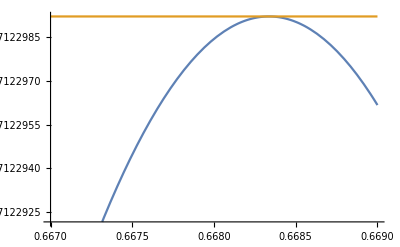

```mathematica
Plot[{f[x],0.7122992135654154},{x,0.667,0.669}]
```

```mathematica
f[x]
```

```mathematica
ρ 2/3 Q^3/.%
```

{(25 c^2 N1^3 π^2)/(3 L (5 c L+5 N1+4 M α)^2)}

```mathematica
%//FullSimplify
```

{(25 c^2 N1^3 π^2)/(3 L (5 c L+5 N1+4 M α)^2)}

```mathematica
Integrate[σ[x]/(c^2+(Λ-x)^2),{x,-Infinity,Infinity},Assumptions->c>0&&Λ>0]
```

```mathematica
-(2 M α)/(4 c^2 L+L Λ^2)+(6 N1)/(9 c^2 L+4 L Λ^2)
```

```mathematica
Integrate[σ[x]/(c^2+(Λ-x)^2),{x,-Infinity,Infinity},Assumptions->c>0&&Λ<0]
```

-(2 M α)/(4 c^2 L+L Λ^2)+(6 N1)/(9 c^2 L+4 L Λ^2)

```mathematica
σ1[Λ_]:=1/(2Pi)(-2c(-(2 M α)/(4 c^2 L+L Λ^2)+(6 N1)/(9 c^2 L+4 L Λ^2))+(4c)/(c^2+4Λ^2)N1/L)
```

```mathematica
%//Simplify
```

{(3 c^2 N1^3 π^2)/(L (3 c L-4 M+6 N1)^2)}

```mathematica
%//FullSimplify
```

{(3 c^2 N1^3 π^2)/(L (3 c L-4 M+6 N1)^2)}

```mathematica
Solve[{2Pi ρ,N1/L}=={1+(5 N1+4 M α)/(5 c L), 2Q ρ},{ρ,Q}]
```

{{ρ→(5 c L+5 N1+4 M α)/(10 c L π),Q→(5 c N1 π)/(5 c L+5 N1+4 M α)}}

```mathematica
Integrate[4/(c^2+4(x)^2),{x,-Infinity,Infinity},Assumptions->c>0]
```

(2 π)/c

```mathematica
Integrate[2/(c^2+(x)^2),{x,-Infinity,Infinity},Assumptions->c>0]
```

(2 π)/c

```mathematica
σ[Λ_]:=1/(2Pi)*(-(2c*α)/(c^2+Λ^2)M/L+(4c)/(c^2+4Λ^2)N1/L)
```

```mathematica
4c*Integrate[σ1[Λ]/(c^2+4Λ^2),{Λ,-Infinity,Infinity}]
```

ConditionalExpression[(2 π (5 N1+4 M α))/(5 c L), Re[c]>0]

```mathematica
Integrate[σ[Λ],{Λ,-Infinity,Infinity}]
```

ConditionalExpression[(-M+N1)/L, Re[c]>0]

```mathematica
Solve[{2Pi σ,2Pi ρ,N1/L,M/L}=={-2B 2/c σ+2Q 4/c ρ,1-2B 4/c σ+2Q 2/c ρ, 2Q ρ, 2B σ},{ρ,Q,B,σ}]
(1+4/c M/L)1/(2Pi)2/3 Q^3/.%

%//Simplify

%//FullSimplify
```

ConditionalExpression[-(2 (2 M-3 N1))/(3 c L), Re[c]>0]

{{ρ→(c L-4 M+2 N1)/(2 c L π),Q→(c N1 π)/(c L-4 M+2 N1),B→-(c M π)/(2 (M-2 N1)),σ→(-M+2 N1)/(c L π)}}

{(c^3 (1+(4 M)/(c L)) N1^3 π^2)/(3 (c L-4 M+2 N1)^3)}

{(c^2 (c L+4 M) N1^3 π^2)/(3 L (c L-4 M+2 N1)^3)}

{(c^2 (c L+4 M) N1^3 π^2)/(3 L (c L-4 M+2 N1)^3)}

```mathematica
Integrate[σ1[x]/(c^2+(Λ-x)^2),{x,-Infinity,Infinity},Assumptions->c>0&&Λ>0]
```

((3 M α)/(9 c^2+Λ^2)+(6 N1)/(9 c^2+4 Λ^2)-(10 N1)/(25 c^2+4 Λ^2))/L

```mathematica
Integrate[σ1[x]/(c^2+(Λ-x)^2),{x,-Infinity,Infinity},Assumptions->c>0&&Λ<0]
```

((3 M α)/(9 c^2+Λ^2)+(6 N1)/(9 c^2+4 Λ^2)-(10 N1)/(25 c^2+4 Λ^2))/L

```mathematica
σ2[Λ_]:=1/(2Pi)(-2c(((3 M α)/(9 c^2+Λ^2)+(6 N1)/(9 c^2+4 Λ^2)-(10 N1)/(25 c^2+4 Λ^2))/L)+(4c)/(c^2+4Λ^2)N1/L)
```

```mathematica
4c*Integrate[σ2[Λ]/(c^2+4Λ^2),{Λ,-Infinity,Infinity}]
```

ConditionalExpression[(35 N1-12 M α)/(21 c L), Re[c]>0]

```mathematica
Solve[{2Pi ρ,N1/L}=={1+(35 N1-12 M α)/(21 c L), 2Q ρ},{ρ,Q}]
```

{{ρ→(21 c L+35 N1-12 M α)/(42 c L π),Q→(21 c N1 π)/(21 c L+35 N1-12 M α)}}

```mathematica
ρ 2/3 Q^3/.%
```

{(147 c^2 N1^3 π^2)/(L (21 c L+35 N1-12 M α)^2)}

```mathematica
%//Reduce
```

Reduce::naqs: (147 c^2 N1^3 π^2)/(L (21 c L+35 N1-12 M α)^2) is not a quantified system of equations and inequalities.

Reduce[{(147 c^2 N1^3 π^2)/(L (21 c L+35 N1-12 M α)^2)}]

```mathematica
σ2[x]
```

((4 c N1)/(L (c^2+4 x^2))-(2 c ((6 N1)/(9 c^2+4 x^2)-(10 N1)/(25 c^2+4 x^2)+(3 M α)/(9 c^2+x^2)))/L)/(2 π)

```mathematica
Integrate[σ2[x]/(c^2+(Λ-x)^2),{x,-Infinity,Infinity},Assumptions->c>0&&Λ<0]
```

(2 (-(2 M α)/(16 c^2+Λ^2)+N1 (3/(9 c^2+4 Λ^2)-5/(25 c^2+4 Λ^2)+7/(49 c^2+4 Λ^2))))/L

```mathematica
σ3[Λ_]:=1/(2Pi)(-2c((2 (-(2 M α)/(16 c^2+Λ^2)+N1 (3/(9 c^2+4 Λ^2)-5/(25 c^2+4 Λ^2)+7/(49 c^2+4 Λ^2))))/L)+(4c)/(c^2+4Λ^2)N1/L)
```

```mathematica
4c*Integrate[σ3[Λ]/(c^2+4Λ^2),{Λ,-Infinity,Infinity}]
```

ConditionalExpression[(21 N1+8 M α)/(18 c L), Re[c]>0]

```mathematica
Solve[{2Pi ρ,N1/L}=={1+(21 N1+8 M α)/(18 c L), 2Q ρ},{ρ,Q}]
```

{{ρ→(18 c L+21 N1+8 M α)/(36 c L π),Q→(18 c N1 π)/(18 c L+21 N1+8 M α)}}

```mathematica
ρ 2/3 Q^3/.%
```

{(108 c^2 N1^3 π^2)/(L (18 c L+21 N1+8 M α)^2)}

```mathematica
Clear[σ,a];
```

```mathematica
σ[Λ_,0]:=1/(2Pi)*(-(2c*α)/(c^2+Λ^2)M/L+(4c)/(c^2+4Λ^2)N1/L);

Integrate[σ[x,0]/(c^2+(Λ-x)^2),{x,-Infinity,Infinity},Assumptions->c>0&&Λ>0]
```

-(2 M α)/(4 c^2 L+L Λ^2)+(6 N1)/(9 c^2 L+4 L Λ^2)

```mathematica
For[i=0,i<5,i++,
Print[i];
a[Λ_,i]:=Integrate[σ[x,i]/(c^2+(Λ-x)^2),{x,-Infinity,Infinity},Assumptions->c>0&&Λ>0];
Print[a[x,i]];
σ[Λ_,i+1]:=1/(2Pi)(-2c(a[Λ,i])+(4c)/(c^2+4Λ^2)N1/L);
Print[σ[x,i+1]];
4c*Integrate[σ[Λ,i+1]/(c^2+4Λ^2),{Λ,-Infinity,Infinity},Assumptions->c>0];
Print[%];
Solve[{2Pi ρ,N1/L}=={1+%, 2Q ρ},{ρ,Q}];
e=2/3 ρ Q^3/.%

]
```

0

(N1-M α)/(c^2 L)

((4 c N1)/(L (c^2+4 x^2))-(2 (N1-M α))/(c L))/(2 π)

-(2 M α)/(4 c^2 L+L Λ^2)+(6 N1)/(9 c^2 L+4 L Λ^2)

ReplaceAll::reps: {-(2 M α)/(4 c^2 L+L Λ^2)+(6 N1)/(9 c^2 L+4 L Λ^2)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of 1/π.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Hold[1/π].

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of 1/(2 π).

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

-(2 M α)/(4 c^2 L+L Λ^2)+(6 N1)/(9 c^2 L+4 L Λ^2)

ReplaceAll::reps: {-(2 M α)/(4 c^2 L+L Λ^2)+(6 N1)/(9 c^2 L+4 L Λ^2)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

2

-(2 M α)/(4 c^2 L+L Λ^2)+(6 N1)/(9 c^2 L+4 L Λ^2)

ReplaceAll::reps: {-(2 M α)/(4 c^2 L+L Λ^2)+(6 N1)/(9 c^2 L+4 L Λ^2)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

3

-(2 M α)/(4 c^2 L+L Λ^2)+(6 N1)/(9 c^2 L+4 L Λ^2)

4

-(2 M α)/(4 c^2 L+L Λ^2)+(6 N1)/(9 c^2 L+4 L Λ^2)

```mathematica
σ[x_,1]:=((4 c N1)/(L (c^2+4 x^2))-(2 (N1-M α))/(c L))/(2 π);
```

```mathematica
b[1]=4c*Integrate[σ[Λ,1]/(c^2+4Λ^2),{Λ,-Infinity,Infinity},Assumptions->c>0]
```

(2 M α)/(c L)

```mathematica
b[1]
```

(2 M α)/(c L)

```mathematica
a[0,x]
```

$Aborted

```mathematica
4c*Integrate[(Subscript[σ, 1][Λ])/(c^2+4Λ^2),{Λ,-Infinity,Infinity},Assumptions->c>0]
```

4 c Integrate[((4 c N1)/(L (c^2+4 Λ^2))-2 c a_5[Λ])/(2 π (c^2+4 Λ^2)),{Λ,-∞,∞},Assumptions→c>0]

```mathematica
Clear[σ]
```

```mathematica
4c*Integrate[σ[Λ,0]/(c^2+4Λ^2),{Λ,-Infinity,Infinity},Assumptions->c>0];
Solve[{2Pi ρ,N1/L}=={1+%, 2Q ρ},{ρ,Q}]
e=2/3 ρ Q^3/.%
```

{{ρ→(3 c L+6 N1-4 M α)/(6 c L π),Q→(3 c N1 π)/(3 c L+6 N1-4 M α)}}

{(3 c^2 N1^3 π^2)/(L (3 c L+6 N1-4 M α)^2)}

```mathematica
a[Λ_,0]:=Integrate[σ[x,0]/(c^2+(Λ-x)^2),{x,-Infinity,Infinity},Assumptions->c>0&&Λ>0];
σ[Λ_,1]:=1/(2Pi)(-2c(a[Λ,0])+(4c)/(c^2+4Λ^2)N1/L);
4c*Integrate[σ[Λ,1]/(c^2+4Λ^2),{Λ,-Infinity,Infinity},Assumptions->c>0];
Solve[{2Pi ρ,N1/L}=={1+%, 2Q ρ},{ρ,Q}]
e=2/3 ρ Q^3/.%
```

{{ρ→(5 c L+5 N1+4 M α)/(10 c L π),Q→(5 c N1 π)/(5 c L+5 N1+4 M α)}}

{(25 c^2 N1^3 π^2)/(3 L (5 c L+5 N1+4 M α)^2)}

```mathematica
a[Λ_,1]:=Integrate[σ[x,1]/(c^2+(Λ-x)^2),{x,-Infinity,Infinity},Assumptions->c>0&&Λ>0];
σ[Λ_,2]:=1/(2Pi)(-2c(a[Λ,1])+(4c)/(c^2+4Λ^2)N1/L);
4c*Integrate[σ[Λ,2]/(c^2+4Λ^2),{Λ,-Infinity,Infinity},Assumptions->c>0];
Solve[{2Pi ρ,N1/L}=={1+%, 2Q ρ},{ρ,Q}]
e=2/3 ρ Q^3/.%
```

{{ρ→(c L+3 N1-2 M α)/(2 c L π),Q→(c N1 π)/(c L+3 N1-2 M α)}}

{(c^2 N1^3 π^2)/(3 L (c L+3 N1-2 M α)^2)}

```mathematica
a[Λ_,2]:=Integrate[σ[x,2]/(c^2+(Λ-x)^2),{x,-Infinity,Infinity},Assumptions->c>0&&Λ>0];
σ[Λ_,3]:=1/(2Pi)(-2c(a[Λ,2])+(4c)/(c^2+4Λ^2)N1/L);
4c*Integrate[σ[Λ,3]/(c^2+4Λ^2),{Λ,-Infinity,Infinity},Assumptions->c>0];
Solve[{2Pi ρ,N1/L}=={1+%, 2Q ρ},{ρ,Q}]
e=2/3 ρ Q^3/.%
```

Integrate::idiv: Integral of (c^2 N1-4 N1 x^2+c^2 M α+4 M x^2 α)/(c^5 L π+4 c^3 L π x^2) does not converge on {-∞,∞}.

$Aborted

{{ρ→(1+$Aborted)/(2 π),Q→(N1 π)/(L (1+$Aborted))}}

{(N1^3 π^2)/(3 L^3 (1+$Aborted)^2)}

```mathematica
σ[x,2]
```

Integrate::idiv: Integral of (c^2 N1-4 N1 x^2+c^2 M α+4 M x^2 α)/(c^5 L π+4 c^3 L π x^2) does not converge on {-∞,∞}.

((4 c N1)/(L (c^2+4 x^2))-2 c Integrate[((4 c N1)/(L (c^2+4 x^2))-(2 (N1-M α))/(c L))/(2 c^2 π),{x,-∞,∞},Assumptions→c>0&&x>0])/(2 π)

```mathematica
a[x,0]
```

(N1-M α)/(c^2 L)

```mathematica
a[Λ_,0]:=Integrate[σ[x,0]/(c^2+(Λ-x)^2),{x,-Infinity,Infinity},Assumptions->c>0]
```

```mathematica
-(2 M α)/(4 c^2 L+L Λ^2)+(6 N1)/(9 c^2 L+4 L Λ^2)//Simplify
```

-(2 M α)/(4 c^2 L+L Λ^2)+(6 N1)/(9 c^2 L+4 L Λ^2)

```mathematica
Clear[a]
```

```mathematica
Integrate[σ[x,0]/(c^2+(Λ-x)^2),{x,-Infinity,Infinity},Assumptions->c>0]
```